# Moran diffusion dynamics

## Fixed population

```mathematica
DSolve[D[f[x]x(1-x),{x,2}]==0,f[x],x]
```

{{f[x]→C[1]/(x-x^2)+C[2]/(1-x)}}

```mathematica
λ/n^2 * D[f[x]x(1-x),{x,2}]==-2 λ μ n DiracDelta[x-1/n]
```

(λ (-2 f[x]+2 (1-2 x) f'[x]+(1-x) x f''[x]))/n^2==-2 n λ μ DiracDelta[-1/n+x]

```mathematica
DSolve[{λ/n^2 * D[f[x]x(1-x),{x,2}]==-2 λ μ n DiracDelta[x-1/n],
f[1]==1},
f[x],{x,0,1}]//Simplify
```

{{f[x]→1/((-1+x) x)(-1+x-2 n^2 (-1+n x) μ HeavisideTheta[(-1+n)/n]+2 n^2 (-1+n x) μ HeavisideTheta[-1/n+x])}}

{{f→Function[{x},1/((-1+x) x)μ (-1+x-2 n^2 (-1+n x) HeavisideTheta[(-1+n)/n]+2 n^2 (-1+n x) HeavisideTheta[-1/n+x])]}}

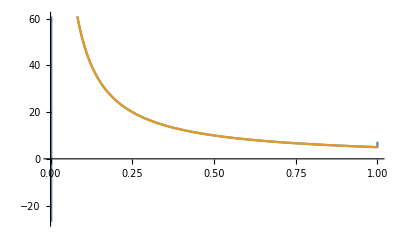

```mathematica
solf=DSolve[{λ/n^2 * D[f[x]x(1-x),{x,2}]==-2 λ μ n DiracDelta[x-1/n],f[1]==μ},f,{x,0,1}]//Simplify
params={n-> 500,μ-> 5};
Plot[{f[x]/.solf/.params,μ/x/.params},{x,0,1}]
```

## Growing population

```mathematica
a[x_,t_]:=γ x E^(-γ t)
b[x_,t_]:=x E^(-2γ t)(2λ(1-x E^(-γ t))+γ)/n0
a[x,t]
b[x,t]
```

ⅇ^(-t γ) x γ

(ⅇ^(-2 t γ) x (γ+2 (1-ⅇ^(-t γ) x) λ))/n0

```mathematica
-D[a[x,t]*f[x],x]+ D[b[x,t]*f[x],{x,2}]/2+2 (λ+γ) μ n0 E^(γ t) DiracDelta[x-1/n]==0
```

2 ⅇ^(t γ) n0 (γ+λ) μ DiracDelta[-1/n+x]-ⅇ^(-t γ) γ f[x]-ⅇ^(-t γ) x γ f'[x]+1/2 ((2 ⅇ^(-2 t γ) (-2 ⅇ^(-t γ) λ f[x]+(γ+2 (1-ⅇ^(-t γ) x) λ) f'[x]))/n0+(ⅇ^(-2 t γ) x (-4 ⅇ^(-t γ) λ f'[x]+(γ+2 (1-ⅇ^(-t γ) x) λ) f''[x]))/n0)==0

```mathematica
ruleParamsGrowth={n0-> 40,μ-> 1.2, γ-> 0.1,λ-> 1};
```

```mathematica
solGrowth[x_]=DSolve[{-D[a[x,t]*f[x],x]+ D[b[x,t]*f[x],{x,2}]/2+2 (λ+γ) μ n0 E^(γ t)DiracDelta[x-1/(n0 E^(γ t))]==0,
f[1]==1},
f[x],{x,0,1}].00.00
```

{{f[x]→((-2 λ+ⅇ^(t γ) (γ+2 λ))^(-√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^(-1/2 √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(-(ⅇ^(2 t γ) n0 γ)/(2 λ)-1/2 √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (λ √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2) √(ⅇ^(t γ) γ-2 λ+2 ⅇ^(t γ) λ) (-2 λ+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)+1/2 √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^(1/2 √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2))+λ √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2) (-2 λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^(1/2 √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) C[1]-λ √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^(1/2 √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) C[1]-2 ⅇ^(4 t γ) n0^2 γ √((ⅇ^(-t γ) (ⅇ^(2 t γ) n0 γ-2 λ+2 ⅇ^(2 t γ) n0 λ))/n0) (-2 λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) μ HeavisideTheta[1-ⅇ^(-t γ)/n0]-2 ⅇ^(4 t γ) n0^2 λ √((ⅇ^(-t γ) (ⅇ^(2 t γ) n0 γ-2 λ+2 ⅇ^(2 t γ) n0 λ))/n0) (-2 λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) μ HeavisideTheta[1-ⅇ^(-t γ)/n0]+2 ⅇ^(4 t γ) n0^2 γ √((ⅇ^(-t γ) (ⅇ^(2 t γ) n0 γ-2 λ+2 ⅇ^(2 t γ) n0 λ))/n0) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)+√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) μ HeavisideTheta[1-ⅇ^(-t γ)/n0]+2 ⅇ^(4 t γ) n0^2 λ √((ⅇ^(-t γ) (ⅇ^(2 t γ) n0 γ-2 λ+2 ⅇ^(2 t γ) n0 λ))/n0) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)+√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) μ HeavisideTheta[1-ⅇ^(-t γ)/n0]-2 ⅇ^(4 t γ) n0^2 γ √((ⅇ^(-t γ) (ⅇ^(2 t γ) n0 γ-2 λ+2 ⅇ^(2 t γ) n0 λ))/n0) (-2 λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)+√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) μ HeavisideTheta[-ⅇ^(-t γ)/n0+x]-2 ⅇ^(4 t γ) n0^2 λ √((ⅇ^(-t γ) (ⅇ^(2 t γ) n0 γ-2 λ+2 ⅇ^(2 t γ) n0 λ))/n0) (-2 λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)+√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) μ HeavisideTheta[-ⅇ^(-t γ)/n0+x]+2 ⅇ^(4 t γ) n0^2 γ √((ⅇ^(-t γ) (ⅇ^(2 t γ) n0 γ-2 λ+2 ⅇ^(2 t γ) n0 λ))/n0) (-2 λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) μ HeavisideTheta[-ⅇ^(-t γ)/n0+x]+2 ⅇ^(4 t γ) n0^2 λ √((ⅇ^(-t γ) (ⅇ^(2 t γ) n0 γ-2 λ+2 ⅇ^(2 t γ) n0 λ))/n0) (-2 λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) (-(2 ⅇ^(-t γ) λ)/n0+ⅇ^(t γ) (γ+2 λ))^((ⅇ^(2 t γ) n0 γ)/(2 λ)) (-2 x λ+ⅇ^(t γ) (γ+2 λ))^(√(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2)) μ HeavisideTheta[-ⅇ^(-t γ)/n0+x]))/(x λ √(((ⅇ^(2 t γ) n0 γ+λ)^2)/λ^2) √(ⅇ^(t γ) γ+2 ⅇ^(t γ) λ-2 x λ))}}

```mathematica
LogPlot[solGrowth[x]/.ruleParamsGrowth/.{t-> 5}/.{C[1]->0},{x,0,1}]
```

-Graphics-

```mathematica
solGrowth[x]/.ruleParamsGrowth/.{C[1]->0}
```

{{f[x]→1/(√((1+4. ⅇ^(0.2 t))^2) x)(-2+2.1 ⅇ^(0.1 t))^(-√((1+4. ⅇ^(0.2 t))^2)) (-1/20 ⅇ^(-0.1 t)+2.1 ⅇ^(0.1 t))^(-1/2 √((1+4. ⅇ^(0.2 t))^2)) (2.1 ⅇ^(0.1 t)-2 x)^(-1/2-2. ⅇ^(0.2 t)-1/2 √((1+4. ⅇ^(0.2 t))^2)) ((-2+2.1 ⅇ^(0.1 t))^(1/2+2. ⅇ^(0.2 t)+1/2 √((1+4. ⅇ^(0.2 t))^2)) (-1/20 ⅇ^(-0.1 t)+2.1 ⅇ^(0.1 t))^(1/2 √((1+4. ⅇ^(0.2 t))^2)) √((1+4. ⅇ^(0.2 t))^2) (2.1 ⅇ^(0.1 t)-2 x)^(√((1+4. ⅇ^(0.2 t))^2))-667.873 ⅇ^(0.4 t) (-2+2.1 ⅇ^(0.1 t))^(√((1+4. ⅇ^(0.2 t))^2)) (-1/20 ⅇ^(-0.1 t)+2.1 ⅇ^(0.1 t))^(2. ⅇ^(0.2 t)) √(ⅇ^(-0.1 t) (-2+84. ⅇ^(0.2 t))) (2.1 ⅇ^(0.1 t)-2 x)^(√((1+4. ⅇ^(0.2 t))^2)) HeavisideTheta[1-ⅇ^(-0.1 t)/40]+667.873 ⅇ^(0.4 t) (-1/20 ⅇ^(-0.1 t)+2.1 ⅇ^(0.1 t))^(2. ⅇ^(0.2 t)+√((1+4. ⅇ^(0.2 t))^2)) √(ⅇ^(-0.1 t) (-2+84. ⅇ^(0.2 t))) (2.1 ⅇ^(0.1 t)-2 x)^(√((1+4. ⅇ^(0.2 t))^2)) HeavisideTheta[1-ⅇ^(-0.1 t)/40]-667.873 ⅇ^(0.4 t) (-2+2.1 ⅇ^(0.1 t))^(√((1+4. ⅇ^(0.2 t))^2)) (-1/20 ⅇ^(-0.1 t)+2.1 ⅇ^(0.1 t))^(2. ⅇ^(0.2 t)+√((1+4. ⅇ^(0.2 t))^2)) √(ⅇ^(-0.1 t) (-2+84. ⅇ^(0.2 t))) HeavisideTheta[-1/40 ⅇ^(-0.1 t)+x]+667.873 ⅇ^(0.4 t) (-2+2.1 ⅇ^(0.1 t))^(√((1+4. ⅇ^(0.2 t))^2)) (-1/20 ⅇ^(-0.1 t)+2.1 ⅇ^(0.1 t))^(2. ⅇ^(0.2 t)) √(ⅇ^(-0.1 t) (-2+84. ⅇ^(0.2 t))) (2.1 ⅇ^(0.1 t)-2 x)^(√((1+4. ⅇ^(0.2 t))^2)) HeavisideTheta[-1/40 ⅇ^(-0.1 t)+x])}}